{{z→InterpolatingFunction[{{0., 120.}}, <>]}}

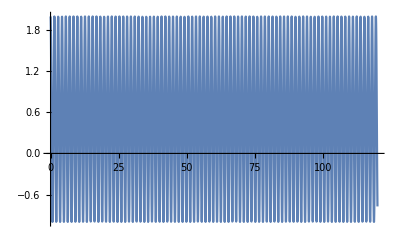

Hanging spring oscillating:

```mathematica
m=1;
l=1;
g=10;
b=2m g;
k=b/l;
ω=Sqrt[k/m];
L=1/2*m*(z'[t]^2)+m*g*(l+z[t])-1/2*(ω^2)*m*(z[t]^2);
Needs["VariationalMethods`"]
eqs=EulerEquations[L,z[t],t];
s=NDSolve[{eqs,z[0]==2,z'[0]==0},z,{t,0,120}]
Plot[Evaluate[z[t]/.s],{t,0,120}]

"Hanging spring oscillating:"
plt=Plot[-50,{x,-0.1,0.1},PlotRange->{-3,0}];
Animate[Show[plt,Graphics[{Line[{{0,0},{0,-(l+z[t])}}]}],Graphics[{Red,Ball[{0,-(l+z[t])},Sqrt[m]/10]}],AspectRatio->Automatic]/.s,{t,0,120},AnimationRate->1, AnimationRunning->False,RefreshRate->120]
```